```mathematica
Clear[f1,g,h,i,j,f3,f,c,d,c1,d1,t,x,x1,x3,x4,wolfram,approx1]
f[t_]:=1/(1+2t)
t1=f[t]/.t-> a;
t2=f[t]/.t-> b;
t3=D[f[t]];
f1[t_]:=Exp[-x t]
f3[t_,x_]:=Exp[-x *t]/(1+2t)
```

```mathematica
(*3 terms approximation, integration by parts, taking into account that the boundary at Infinite should be neglected as we can see above*)
```

```mathematica
a=0;
```

```mathematica
x4[0]=f[t]
```

1/(1+2 t)

```mathematica
x3[0]=Integrate[f1[t],t]
```

-ⅇ^(-t x)/x

```mathematica
For[i=0,i<4,i++,x3[i+1]=Integrate[x3[i],t]];
```

```mathematica
For[i=0,i<4,i++,x4[i+1]=D[x4[i],t]];
```

We introduce the (-1) factor as by studying the integral by parts of f3, we observe how due to the contribution given by the upper bound being neglected the term at a dominates the iteration.

```mathematica
w[i_]:=(-1)^(i+1)x4[i]x3[i]
```

```mathematica
approx1[x_]:=Sum[w[i],{i,0,2}]
```

```mathematica
approx=approx1[x]/.t-> 0
```

8/x^3-2/x^2+1/x

```mathematica
wolfram=AsymptoticIntegrate[Exp[-x *t]/(1+2t),{t,0,Infinity},{x,Infinity,3}](*Exact Soluton by wolfram*)
```

8/x^3-2/x^2+1/x

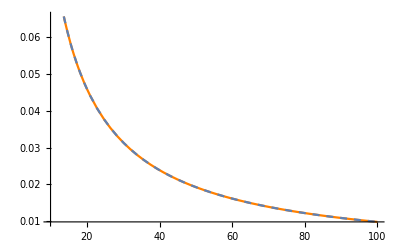

```mathematica
Show[Plot[approx,{x,10,100},PlotStyle->Orange],Plot[wolfram,{x,10,100},PlotStyle->Dashed]]
```

```mathematica
Limit[wolfram,x-> Infinity]
```

0

```mathematica
Limit[approx,x-> Infinity]
```

0

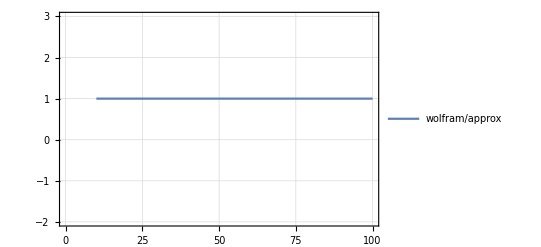

```mathematica
Plot[wolfram/approx,{x,10,100},PlotTheme->"Detailed",PlotRange->{-2,3}]
```